```mathematica
f=Interpolation[{{0,-1},{1,2},{3,0},{4,1}}]
```

```mathematica
Plot[f[x],{x,-1,6}]
```

```mathematica
Show[%,ListPlot[{{0,-1},{1,2},{3,0},{4,1}}]]
```

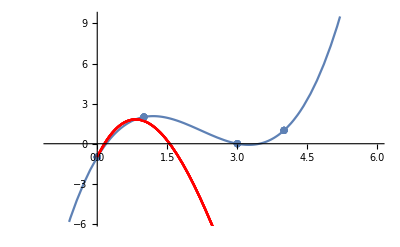

```mathematica
Show[%,ListPlot[{{0,-1},{1,2},{3,0},{4,1}}],Plot[(1/2)*x^3-(10/2)*x^2+(36/5)*x-1,{x,0,6},PlotStyle->Red],PlotLegends->LineLegend["Expressions"]]
```